# Differential Equations for High School Students

Kyungwon Chun, BioBrain Inc.
kwchun@biobrain.kr

```mathematica
DateString[]
$Version
```

Mon 15 Apr 2019 13:29:35

11.3.0 for Mac OS X x86 (64-bit) (March 7, 2018)

## Course Overview

Instructor: Kyungwon Chun

101 of Wolfram Language, and MathSymbolica

We will investigate various dynamics based on differential equations.

Lecture materials will be uploaded to GitHub(https://github.com/ruddyscent/de4gsa.git)

## Before We Start

Make a Wolfram user account at Wolfram User Portal.

Download the recent version of Mathematica.

Install Mathematica on your computer.

## Fun Facts

### Mathematica 1.0 was released in June 1988.

#### References

Wolfram 언어 버전 기록

### Steve Jobs suggested the name, “Mathematica.”

-Graphics-

#### References

A Few Memories

### Wolfram’s R&D staffs involved to provide Mathematical aspects in the Numb3rs.

-Graphics-

#### References

The Math behind Numb3rs

### The language was officially named only in June 2013.

-Graphics-

#### References

Wolfram Language

### Both Stephen Wolfram and his son Christopher Wolfram were involved in helping create the alien language for the film Arrival, for which they used the Wolfram Language.

-Graphics-

#### References

How Arrival’s Designers Crafted a Mesmerizing Language

### Mathematica is bundled for free on NeXT, Raspberry Pi, Intel Edison.

-Graphics-

#### References:

Steve Jobs: A Few Memories

Wolfram to Bring World’s Most Sophisticated Programming Language to New Intel SD-Card-Sized Computer

Wolfram + Raspberry Pi Project: A Wolfram Engine on Every Raspberry Pi

## We Will Cover

[1] S. Wolfram, An Elementary Introduction to the Wolfram Language, 2nd ed. Wolfram Media, Inc., 2017.

-Graphics-

[2] W. E. Boyce and R. C. DiPrima, Elementary Differential Equations and Boundary Value Problems, 10th ed. Wiley, 2012.

-Graphics-

[3] William E. Boyce, Richard C. DiPrima, and Douglas B. Meade, Elementary Differential Equations, 11th ed. Wiley, 2017.

-Graphics-

## At Day 01

Document-Based Workflow: 
A live coding session to introduce a practical document-based workflow

-Graphics-
https://www.wolfram.com/mathematica/compare-mathematica/index.en.html?footer=lang #workflow

Where is the nearest weather station from Gwangju Science Academy for the Gifted?

-Graphics-

To measure a distance, we require the geographical location of GSA. Even you don’t know anything about the Wolfram Language; you can ask Mathematica to show the geographical location of GSA using a natural language.

Gwangju Science Academy for the Gifted

WolframAlphaQueryResults

```mathematica
gsa=GeoPosition[{35.2282914,126.8462723}]
```

GeoPosition[{35.2283,126.846}]

Wolfram Language provides a command, in the form of a function, to display a geographical location on a map. With knowledge of display directives and options, we can get a fine-tuned map of GSA.

```mathematica
gsa
GeoGraphics[{{Blue,PointSize[.02],Point@%},GeoStyling[Opacity[0]],GeoDisk[%,Quantity[1, "Kilometers"]]},GeoScaleBar->{"Imperial", "Metric"}]
```

GeoPosition[{35.2283,126.846}]

-Graphics-

From the previous example, we can find a way to use functions, lists, a shortcut to the previous result, prefix functions, graphics directives, function options.

The page about WeatherData in The Documentation Center shows how to get the list of n nearest weather stations.

```mathematica
gsa
WeatherData[{%,5}]
```

GeoPosition[{35.2283,126.846}]

{WMO47156,RKJB,WMO47165,WMO47146,RKJK}

The braces with comma separated elements show the most famous data structure in Wolfram Language; List. Also, an element in a square is an object called Entity. This Entity is a class of WeatherStation Entity. Let’s figure out the properties we can use.

```mathematica
Entity["WeatherStation","WMO47156"]//EntityProperties
```

{coordinates,latitude,longitude,name,position}

We can use these properties in the similar form of a function call.

```mathematica
{Entity["WeatherStation","WMO47156"]["Name"],Entity["WeatherStation","WMO47156"]["Position"]}
```

{WMO47156,GeoPosition[{35.167,126.883}]}

The location of the weather station, WMO47156 can be displayed in the same way which we used to display the location of GSA.

```mathematica
GeoGraphics[{Red,PointSize[.02],Point@Entity["WeatherStation","WMO47156"]["Position"]}]
```

-Graphics-

It is not so different to display more than one location on a map.

```mathematica
GeoGraphics[{PointSize[.02],Blue,Point@gsa,Red,Point@Entity["WeatherStation","WMO47156"]["Position"]}]
```

-Graphics-

If we need to plot a bunch of locations on a map, a more appropriate way is required rather than merely list them up manually. The first trial, although the most not-recommended way is

```mathematica
weatherStation=WeatherData[{gsa,5}]
```

{WMO47156,RKJB,WMO47165,WMO47146,RKJK}

```mathematica
stationPosition={};
For[i=1,i≤ Length@weatherStation,i++,AppendTo[stationPosition,weatherStation⟦i⟧["Position"]]]
```

```mathematica
GeoGraphics@Point@stationPosition
```

-Graphics-

With a functional approach, the command becomes much more simplified.

```mathematica
GeoGraphics@Point@Table[s["Position"],{s,weatherStation}]
```

-Graphics-

One of the advantages of a functional approach is that it is easy to apply a parallel computation.

```mathematica
GeoGraphics@Point@ParallelTable[s["Position"],{s,weatherStation}]
```

-Graphics-

The number of kernels which you can use for parallel computation is limited by the number of CPU cores on your device, your license, or your configuration.

-Graphics-

It’s not hard to figure it out which point indicate which weather station, because the list is sorted in ascending order of distance from GIST. However, annotating them is not a bad idea.

```mathematica
GeoGraphics@Table[Tooltip[GeoMarker@s["Position"],s["Name"]],{s,weatherStation}]
```

-Graphics-

Let’s put them all codes together.

```mathematica
GeoGraphics[{Table[Tooltip[GeoMarker[s["Position"],"Color"->Blue],s["Name"]],{s,weatherStation}],Tooltip[GeoMarker[gsa,"Color"->Red],"Gwangju Science Academy for the Gifted"]},GeoScaleBar->{"Imperial", "Metric"}]
```

-Graphics-

Our code looks a little bit lengthy and cryptic. However, if you are trained to find a pattern, probably yes, you can see a repeated pattern in the command. In computer programming, the repeated part is better to be replaced by a function.

```mathematica
geoPrimitive[geoEntity_,color_]:=Tooltip[GeoMarker[geoEntity["Position"],"Color"->color],geoEntity["Name"]]
geoPrimitive[gsa,color_]:=Tooltip[GeoMarker[gsa,"Color"->color],"Gwangju Science Academy for the Gifted"]
```

```mathematica
GeoGraphics[{Table[geoPrimitive[s,Blue],{s,weatherStation}],
geoPrimitive[gsa,Red]},GeoScaleBar->{"Imperial", "Metric"}]
```

-Graphics-

Though Table is the most popular function in Wolfram Language, we will replace it to make the code simpler with two important concepts: a pure function and Map.

A pure function is a handy way to make a temporary function. It is not necessary to suffer from naming functions and arguments. The ‘pure’ in the name means that it has only a function body, not a heading or name. For example, if we want to make a blue marker version of our geoPrimitive:

```mathematica
redGeoPrimitive[entity_]:=geoPrimitive[entity,Red]
```

Instead of the previous formal function definition,

```mathematica
geoPrimitive[#,Red]&
```

geoPrimitive[#1,Red]&

is enough for our purpose. Any names for a new function and its argument are required at all. #, is called a slot, replaces a named argument. & indicates the end of a function body.

Though we can apply the pure function version of redGeoPrimitive to GIST entity, it seems that there is no advantage to do that. However, in the case of the entity list for weather stations, the story is totally different. Before tackling the case, let me introduce a new command, Map. Map is a handy way to apply a function to elements of a list.

If you want to apply the red version of geoPrimitive function to the entity elements in the weatherStation list, not the list itself,

```mathematica
Map[geoPrimitive[#,Red]&,weatherStation]
```

{GeoMarker[GeoPosition[{35.167,126.883}],Color→RGBColor[1, 0, 0]],GeoMarker[GeoPosition[{34.991,126.383}],Color→RGBColor[1, 0, 0]],GeoMarker[GeoPosition[{34.817,126.383}],Color→RGBColor[1, 0, 0]],GeoMarker[GeoPosition[{35.817,127.15}],Color→RGBColor[1, 0, 0]],GeoMarker[GeoPosition[{35.899,126.622}],Color→RGBColor[1, 0, 0]]}

Cool. Moreover, the Map function is used frequently in Wolfram Language, so it provides a short-hand notation, /@. The following command has the same meaning to the previous command.

```mathematica
geoPrimitive[#,Red]&/@weatherStation
```

{GeoMarker[GeoPosition[{35.167,126.883}],Color→RGBColor[1, 0, 0]],GeoMarker[GeoPosition[{34.991,126.383}],Color→RGBColor[1, 0, 0]],GeoMarker[GeoPosition[{34.817,126.383}],Color→RGBColor[1, 0, 0]],GeoMarker[GeoPosition[{35.817,127.15}],Color→RGBColor[1, 0, 0]],GeoMarker[GeoPosition[{35.899,126.622}],Color→RGBColor[1, 0, 0]]}

Eventually, we ready to write the final version of the map generation command.

```mathematica
GeoGraphics[{geoPrimitive[#,Blue]&/@weatherStation,
geoPrimitive[gsa,Red]
},GeoScaleBar->{"Imperial", "Metric"}]
```

-Graphics-

We get a shorter, simpler code without any redundant parts. In the same time, it is scalable and easy to modify. I can not miss mentioning that the output is user-interactable.

The location of weather stations around GIST is apparent now. The next step is to get the weather data from the weather station. The most recent measured temperature from the weather station in downtown Gwangju is

```mathematica
WeatherData["WMO47156","Temperature"]
```

-0.2 °C

Or the whole list of measured temperature in March is

```mathematica
data=WeatherData["WMO47156","Temperature",{2019,4}];
```

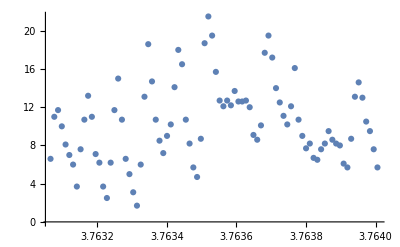

```mathematica
data//ListPlot
```

The temperature distribution using dots make it hard to find a pattern in the data. Fortunately, there is a perfect function for our purpose. DateListPlot connects the data with a line in a sequential manner, and use proper ticks to show the dates of data clearly.

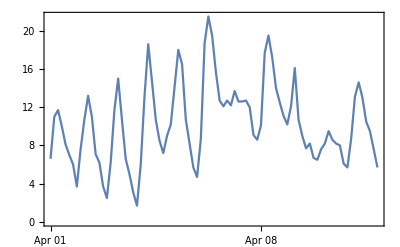

```mathematica
data//DateListPlot
```

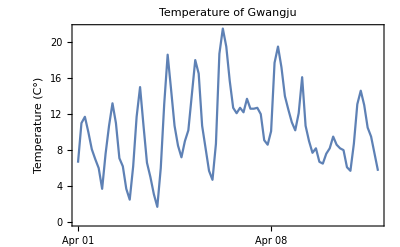

```mathematica
DateListPlot[data,FrameLabel->{"","Temperature (C°)"},PlotLabel->"Temperature of Gwangju",GridLines->Automatic]
```

We can observe the daily variance of temperature.

```mathematica
FindPeaks[data]//Normal
```

{{Mon 1 Apr 2019 06:00:00GMT+9.,11.7},{Tue 2 Apr 2019 06:00:00GMT+9.,13.2},{Wed 3 Apr 2019 06:00:00GMT+9.,15},{Thu 4 Apr 2019 06:00:00GMT+9.,18.6},{Fri 5 Apr 2019 06:00:00GMT+9.,18},{Sat 6 Apr 2019 06:00:00GMT+9.,21.5},{Sun 7 Apr 2019 03:00:00GMT+9.,13.7},{Mon 8 Apr 2019 06:00:00GMT+9.,19.5},{Tue 9 Apr 2019 03:00:00GMT+9.,16.1},{Wed 10 Apr 2019 06:00:00GMT+9.,9.5},{Thu 11 Apr 2019 06:00:00GMT+9.,14.6}}

```mathematica
FindPeaks[-data]//Normal
```

{{Mon 1 Apr 2019 00:00:00GMT+9.,-6.6},{Mon 1 Apr 2019 21:00:00GMT+9.,-3.7},{Tue 2 Apr 2019 21:00:00GMT+9.,-2.5},{Wed 3 Apr 2019 21:00:00GMT+9.,-1.7},{Thu 4 Apr 2019 18:00:00GMT+9.,-7.2},{Fri 5 Apr 2019 21:00:00GMT+9.,-4.7},{Sat 6 Apr 2019 18:00:00GMT+9.,-12.1},{Sun 7 Apr 2019 21:00:00GMT+9.,-8.6},{Mon 8 Apr 2019 21:00:00GMT+9.,-10.2},{Tue 9 Apr 2019 21:00:00GMT+9.,-6.5},{Wed 10 Apr 2019 21:00:00GMT+9.,-5.7},{Thu 11 Apr 2019 21:00:00GMT+9.,-5.7}}

It will be fun to predict the temperature of today from last month temperature.

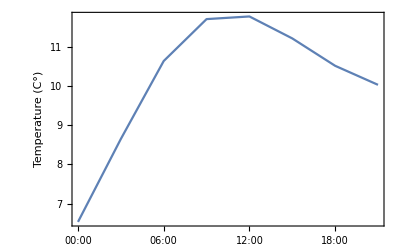

```mathematica
tsm=TimeSeriesModelFit[data];
DateListPlot[TimeSeriesForecast[tsm,{8}],GridLines->Automatic,FrameLabel->{Automatic,"Temperature (C°)"}]
```

If you are familiar to the recent de facto standard data format in the data science field, called dataframe, Dataset will suffice your needs.

```mathematica
data//Normal//Map[Association["Date"->#⟦1⟧,"Temperature"->#⟦2⟧]&,#]&//Dataset
```

Dataset[<>]

At the end of your exploration, you might want to export data or any results.

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/kwchun/BioBrain Dropbox/Kyungwon Chun/Presentations/2019/2019.04.01

```mathematica
Export["WMO47156_Temperature.csv",WeatherData["WMO47156","Temperature",{2019,3}],"CSV"]
```

WMO47156_Temperature.csv